```mathematica
target[x_]:=1+x+x^2
range={-2*Pi, 2*Pi, 0.1};
```

```mathematica
xVals=Range@@range;
funcFromVals[vals_][x_]:=Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x]
```

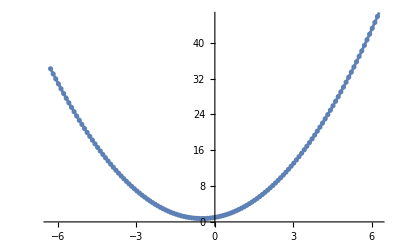

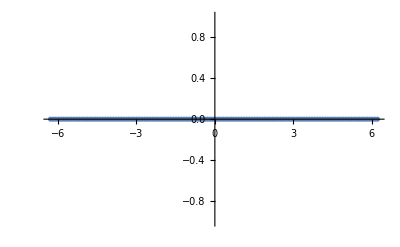

```mathematica
approxVals=(0&)/@xVals;
funcVals=target/@xVals;

PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}]], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}]}]

PlotVals[funcVals]
PlotVals[approxVals]
```

InterpolatingFunction::dmval: Input value {11.5446} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {11.2306} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {10.9221} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

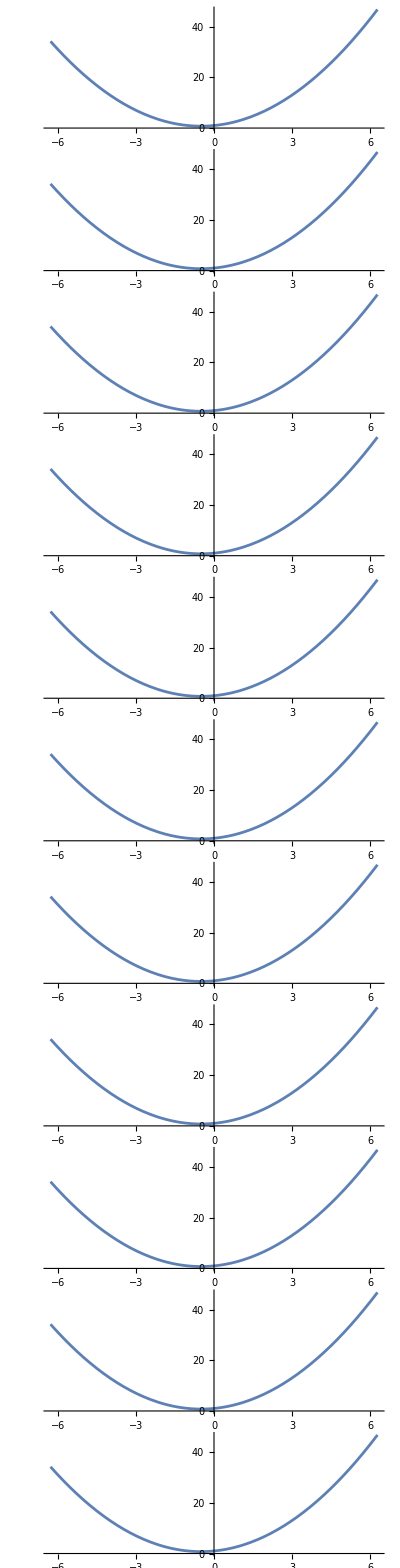

```mathematica
plots={};
Table[Table[
approxFunc=funcFromVals[approxVals];
nestedApproxVals=approxFunc[approxFunc[#]]&/@xVals;
deltaVals=funcVals-nestedApproxVals;
newApproxVals=approxVals+0.1*deltaVals;
approxVals=newApproxVals;,{j, 20}];
plots=AppendTo[plots,Plot[approxFunc[approxFunc[x]], {x, range[[1]], range[[2]]}]];
, {i,0, 10}];

Column@plots
```

InterpolatingFunction::dmval: Input value {11.5438} lies outside the range of data in the interpolating function. Extrapolation will be used.

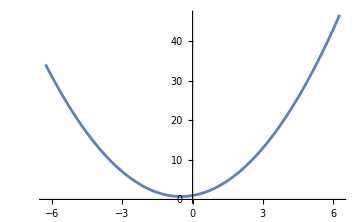
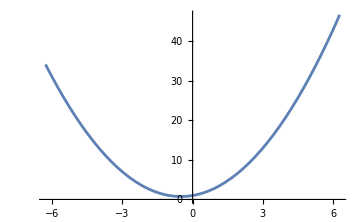
-Graphics-approx-Graphics-target

```mathematica
Row[{Labeled[Plot[approxFunc[approxFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Medium], "approx"], Labeled[Plot[target[x], {x, range[[1]], range[[2]]}, ImageSize->Medium], "target"]}]
```